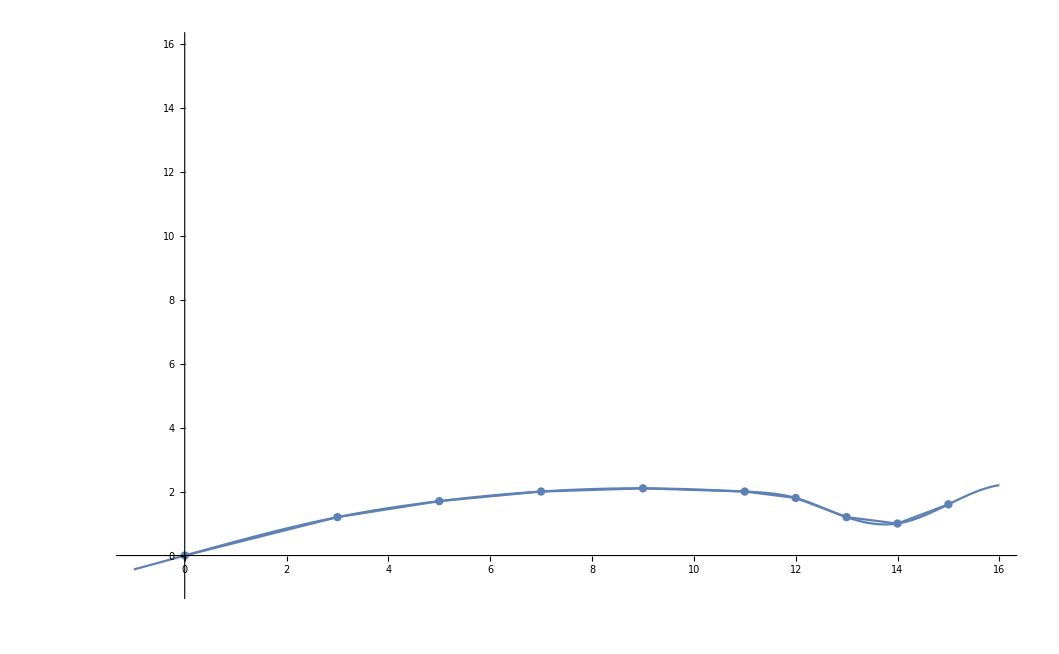

```mathematica
x={0,3,5,7,9,11,12,13,14,15};
y={0,1.2,1.7,2.0,2.1,2.0,1.8,1.2,1.0,1.6};
list = Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.8\\python\\output.txt","list"];
points=Table[{list[[i]],list[[i+1]]},{i,1,Length[list],2}];
Show[ListPlot[points,Joined->True],ListPlot[Table[{x[[i]],y[[i]]},{i,1,Length[x]}],Joined->True,InterpolationOrder->1,Mesh->Full],PlotRange->{{-1,16},{-1,16}}]
```